## Seasonal Ricker model - EWS in rb - Singles

## Setup and Universal Parameters

```mathematica
(* set directory *)
SetDirectory["/Users/tbury/Google Drive/Research/doctorate/critical_transitions_18/ews_seasonal/models_ricker/ricker_seasonal_coe"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* system parameters *)
rw=0.4;
bl=-0.1;
bh=2.24;
```

## Import Data

```mathematica
(* Name of simluation run *)
simName="tmax1000_rwp4";
```

```mathematica
(* Import EWS DataFrame *)
dfEws=Import["data_export/trans_rb/"<>simName<>"/ews_singles.csv"];
```

```mathematica
(* Import power spectrum DataFrame *)
dfPspec=Import["data_export/trans_rb/"<>simName<>"/pspec.csv"];
```

```mathematica
(* Import ews means DataFrame *)
dfEwsMeans=Import["data_export/trans_rb/"<>simName<>"/ews_means.csv"];
```

```mathematica
(* Import ews sd DataFrame *)
dfEwsSd=Import["data_export/trans_rb/"<>simName<>"/ews_deviations.csv"];
```

```mathematica
(* Import Kendall tau values *)
dfKtau=Import["data_export/trans_rb/"<>simName<>"/ktau.csv"];
```

```mathematica
numSims=Length[Union[dfEws[[2;;,1]]]]
```

20

```mathematica
(* Realisation number to display *)
displayNum=6;
```

## Figure params

```mathematica
(* Figure params *)
imgs=400; (* image size *)
aRatio=0.25; (* aspect ratio *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={30,5,5,5};  (* image padding *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos=Scaled[{0.033,0.86}] ;(* panel letter label *)
labelLetterPosSize=12;
lt=0.0075; (* line thickness *)
ls=11; (* label style *)
ps=0.03; (* point size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
textPos=Scaled[{0.03,0.12}]; (* position of text lablel *)
```

## Trajectory Plots

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* Extract info *)
seriesB = Cases[dfEws[[2;;,{1,2,3,4}]],{displayNum,"Breeding",_,_}][[;;,{3,4}]];
seriesNB = Cases[dfEws[[2;;,{1,2,3,4}]],{displayNum,"Non-breeding",_,_}][[;;,{3,4}]];
(*seriesTotal= Cases[dfEws[[2;;,{1,2,3,4}]],{displayNum,"Total",_,_}][[;;,{3,4}]];*)
```

```mathematica
(* Useful info *)
tVals=seriesB[[;;,1]];
tmax=tVals[[-1]];
dt2=tVals[[2]]-tVals[[1]];
windowComps=rw*tmax/dt2-1;
realMax=Max[dfEws[[;;,1]]][[1]];
stateVals=Union[dfEws[[2;;,2]]];
```

```mathematica
(* line legend *)
trajLegend=LineLegend[TMBcolours[[1;;2]],{"Breeding","Non-breeding"},Spacings->{0,0.2},LabelStyle->10]
```

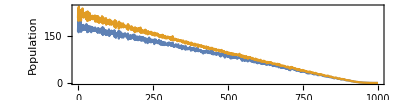

```mathematica
(* plot of breeding series *)
plotPop = ListPlot[{seriesB,seriesNB},
Joined->True,
LabelStyle->12,
PlotLegends->Placed[trajLegend,Scaled[{0.85,0.7}]],
ImageSize->imgs,
LabelStyle->12,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
AspectRatio->aRatio,
ImagePadding->{{padLeft,padRight},{padBottom,40}},
AxesLabel->{"t","Population"},
PlotRange->{{0,tmax},All}]
```

### Output

```mathematica
rTicks=Range[bl,bh,0.2];
rTicksT=(rTicks-bh)*tmax/(bl-bh);
```

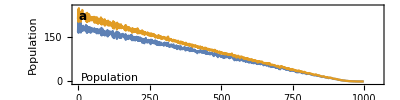

```mathematica
plotTraj=Show[{plotPop},
PlotRange->{{0,tmax*1.05},{-5,250}},
ImageSize->imgs,
LabelStyle->12,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
FrameLabel->{{None,None},{None,"Breeding growth rate, r_b"}},
AspectRatio->aRatio,
ImagePadding->{{padLeft,padRight},{padBottom,40}},
FrameTicks->{{Automatic,Automatic},{Automatic,Transpose[{rTicksT,rTicks}]}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->{Text[Style["a",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Population",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}]}
]
```

## EWS Plots (single realisations)

### Variance

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Variance"][[1,1]];
```

```mathematica
ewsVals=Table[Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}],{state,stateVals}][[;;,;;,{3,4}]];
```

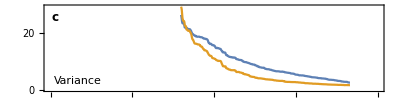

```mathematica
(* Plot EWS *)
plotVar=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Variance",ls],textPos,{-1,0}]}]
```

### Coefficient of variation

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Coefficient of variation"][[1,1]];
```

```mathematica
ewsVals=Table[Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}],{state,stateVals}][[;;,;;,{3,4}]];
```

```mathematica
ewsVals//Dimensions
```

{2,1000,2}

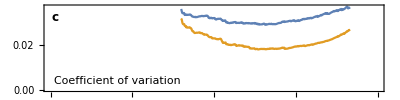

```mathematica
(* Plot EWS *)
plotCv=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Coefficient of variation",ls],textPos,{-1,0}]}]
```

### Smax/Var

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Smax/Var"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

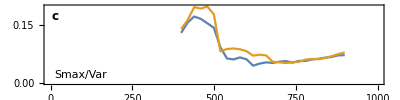

```mathematica
(* Plot EWS *)
plotSmaxVar=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{{"",""},{"Time (generation)",""}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Smax/Var",ls],textPos,{-1,0}]}]
```

### Skewness

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Skewness"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

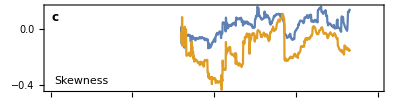

```mathematica
(* Plot EWS *)
plotSkew=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Skewness",ls],textPos,{-1,0}]}]
```

### Kurtosis

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Kurtosis"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

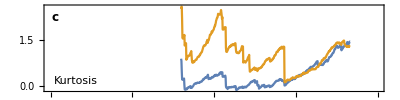

```mathematica
(* Plot EWS *)
plotKurt=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Kurtosis",ls],textPos,{-1,0}]}]
```

### Lag-1 AC

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Lag-1 AC"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

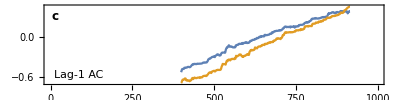

```mathematica
(* Plot EWS *)
plotAc1=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameLabel->{{"",""},{"Time (arbitrary units)",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom*10,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Lag-1 AC",ls],textPos,{-1,0}]}]
```

### Lag-2 AC

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Lag-2 AC"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

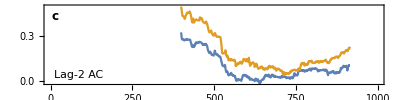

```mathematica
(* Plot EWS *)
plotAc2=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameLabel->{{"",""},{"Time (arbitrary units)",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom*10,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Lag-2 AC",ls],textPos,{-1,0}]}]
```

### Lag-3 AC

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Lag-3 AC"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

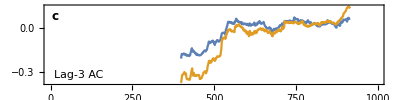

```mathematica
(* Plot EWS *)
plotAc3=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameLabel->{{"",""},{"Time (generation)",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom*10,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Lag-3 AC",ls],textPos,{-1,0}]}]
```

## Kendall Tau Plots

```mathematica
(* figure parameters *)
aRatioBox=1.5;
imgsBox=100;
padBox={{5,30},{5,5}};
ktauTextPos=Scaled[{0.05,0.12}];
ktauText=Text[Style["Kendall τ",ls],ktauTextPos,{-1,0}];
outliers=True;
labelLetterPosBox=Scaled[{0.07,0.86}];
```

### Variance

```mathematica
indexKtau=Position[dfKtau[[1]],"Variance"][[1,1]]
```

6

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | -0.985587 | -0.993644 | -0.993588 | -0.993361 | -0.992396 | -0.993191 | -0.987686 | -0.993531 | -0.99302 | -0.99007 | -0.99075 | -0.987743 | -0.985189 | -0.991772 | -0.989899 | -0.994496 | -0.99285 | -0.992169 | -0.992453 | -0.994666 | -0.991715 | -0.993134 | -0.987402 | -0.986324 | -0.993531 | -0.992793 | -0.984679 | -0.991658 | -0.991431 | -0.99285 | -0.989786 | -0.990183 | -0.990126 | -0.99302 | -0.990523 | -0.995574 | -0.987232 | -0.993701 | -0.992056 | -0.99075 | -0.99546 | -0.984906 | -0.988594 | -0.984849 | -0.993474 | -0.993758 | -0.995177 | -0.992964 | -0.993815 | -0.991375 | -0.992623 | -0.991942 | -0.990013 | -0.989729 | -0.989105 | -0.992056 | -0.994042 | -0.993077 | -0.992056 | -0.994098 | -0.994325 | -0.993644 | -0.988537 | -0.992793 | -0.993077 | -0.993871 | -0.991034 | -0.991204 | -0.99495 | -0.990807 | -0.987005 | -0.994382 | -0.991999 | -0.990467 | -0.991772 | -0.991204 | -0.99058 | -0.995687 | -0.991999 | -0.992226 | -0.990523 | -0.990807 | -0.993304 | -0.990864 | -0.993758 | -0.990013 | -0.991545 | -0.991204 | -0.984849 | -0.987629 | -0.992623 | -0.993361 | -0.985473 | -0.992226 | -0.991318 | -0.993758 | -0.992566 | -0.993418 | -0.990353 | -0.993928
Non-breeding | -0.990467 | -0.989729 | -0.99268 | -0.986722 | -0.981331 | -0.985984 | -0.989048 | -0.976791 | -0.98587 | -0.970719 | -0.968506 | -0.941382 | -0.988991 | -0.976621 | -0.986722 | -0.982693 | -0.975145 | -0.980253 | -0.975145 | -0.987402 | -0.991772 | -0.986041 | -0.972195 | -0.979912 | -0.967882 | -0.989332 | -0.977585 | -0.974805 | -0.975089 | -0.983884 | -0.970889 | -0.975145 | -0.989786 | -0.982579 | -0.9878 | -0.981671 | -0.95903 | -0.980593 | -0.982806 | -0.982068 | -0.982636 | -0.95483 | -0.986495 | -0.972195 | -0.980082 | -0.990296 | -0.98065 | -0.989389 | -0.983884 | -0.987573 | -0.947397 | -0.983771 | -0.978664 | -0.975543 | -0.981841 | -0.945297 | -0.98065 | -0.972308 | -0.974862 | -0.983601 | -0.986041 | -0.989672 | -0.981274 | -0.979572 | -0.984622 | -0.986949 | -0.981955 | -0.966123 | -0.990013 | -0.979004 | -0.943538 | -0.96425 | -0.985927 | -0.98292 | -0.987346 | -0.989162 | -0.968109 | -0.9857 | -0.974408 | -0.99302 | -0.986097 | -0.979118 | -0.976961 | -0.984735 | -0.991829 | -0.977926 | -0.986722 | -0.986438 | -0.985416 | -0.965612 | -0.986949 | -0.986041 | -0.987573 | -0.921748 | -0.988367 | -0.989445 | -0.988708 | -0.987289 | -0.973386 | -0.964307

```mathematica
(* Box plot *)
boxVar=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Coefficient of variation

```mathematica
indexKtau=Position[dfKtau[[1]],"Coefficient of variation"][[1,1]]
```

4

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.662761 | 0.781246 | 0.868804 | 0.831295 | 0.716045 | 0.944333 | 0.901603 | 0.866534 | 0.712527 | 0.907221 | 0.847411 | 0.616059 | 0.587232 | 0.783459 | 0.865343 | 0.796737 | 0.80105 | 0.907051 | 0.892297 | 0.805476 | 0.836686 | 0.469201 | 0.881629 | 0.913179 | 0.635182 | 0.361101 | 0.911477 | 0.904838 | 0.756277 | 0.707533 | 0.867102 | 0.914938 | 0.834076 | 0.378352 | 0.777046 | 0.598865 | 0.511193 | 0.88004 | 0.815633 | 0.91403 | 0.882537 | 0.785445 | 0.871301 | 0.929408 | 0.813988 | 0.618045 | -0.458703 | 0.508242 | 0.602781 | 0.872152 | 0.601816 | 0.739594 | 0.885828 | 0.903362 | 0.643808 | 0.727394 | 0.558803 | 0.108526 | 0.747085 | 0.697546 | 0.883898 | 0.632118 | 0.891502 | 0.14229 | 0.867329 | 0.757356 | 0.616002 | 0.919194 | 0.886168 | 0.67411 | 0.745212 | -0.00575968 | 0.853993 | 0.790722 | 0.685345 | 0.894453 | 0.813477 | 0.826926 | 0.86608 | 0.612711 | 0.883274 | 0.647156 | 0.891048 | 0.864378 | 0.493432 | 0.866931 | 0.894453 | 0.788509 | 0.915279 | 0.939225 | 0.816655 | 0.109547 | 0.667698 | 0.6 | 0.661399 | 0.667868 | 0.833735 | 0.707987 | 0.705717 | 0.88997
Non-breeding | 0.800426 | 0.889403 | 0.890708 | 0.79895 | 0.837027 | 0.942176 | 0.916527 | 0.695957 | 0.898879 | 0.92555 | 0.829536 | 0.825848 | 0.697035 | 0.818017 | 0.862335 | 0.849908 | 0.847978 | 0.935934 | 0.813818 | 0.953752 | 0.632345 | 0.899674 | 0.843893 | 0.870677 | 0.878451 | 0.782778 | 0.949894 | 0.974237 | 0.842644 | 0.785558 | 0.922315 | 0.843666 | 0.904327 | 0.912271 | 0.873344 | 0.918854 | 0.869939 | 0.72711 | 0.891105 | 0.883615 | 0.875614 | 0.877486 | 0.9327 | 0.939396 | 0.780338 | 0.682678 | 0.288977 | 0.565953 | 0.81308 | 0.885941 | 0.698397 | 0.926344 | 0.836232 | 0.893488 | 0.61169 | 0.660718 | 0.672294 | 0.613789 | 0.768308 | 0.942857 | 0.914768 | 0.971514 | 0.956136 | 0.605958 | 0.936104 | 0.907391 | 0.838105 | 0.95466 | 0.931905 | 0.822443 | 0.874308 | 0.8347 | 0.581614 | 0.900014 | 0.954717 | 0.95483 | 0.922826 | 0.881685 | 0.938942 | 0.926344 | 0.953242 | 0.898369 | 0.960051 | 0.809618 | 0.936729 | 0.897404 | 0.677458 | 0.932189 | 0.828458 | 0.960959 | 0.950291 | 0.693801 | 0.688012 | 0.834813 | 0.76774 | 0.871017 | 0.906937 | 0.839864 | 0.863413 | 0.931962

```mathematica
(* Box plot *)
boxCv=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Lag-1 Autocorrelation

```mathematica
indexKtau=Position[dfKtau[[1]],"Lag-1 AC"][[1,1]]
```

5

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.844176 | 0.954547 | 0.960278 | 0.966236 | 0.955455 | 0.943198 | 0.952958 | 0.968279 | 0.955114 | 0.935594 | 0.943935 | 0.945865 | 0.898312 | 0.953582 | 0.94002 | 0.916243 | 0.960108 | 0.94524 | 0.954717 | 0.887814 | 0.904724 | 0.939963 | 0.966804 | 0.952844 | 0.901376 | 0.942744 | 0.953412 | 0.958689 | 0.958916 | 0.953298 | 0.97577 | 0.905916 | 0.942744 | 0.969698 | 0.94456 | 0.925379 | 0.942403 | 0.936331 | 0.954547 | 0.899787 | 0.954206 | 0.963569 | 0.915676 | 0.971854 | 0.95937 | 0.941439 | 0.894794 | 0.95449 | 0.936785 | 0.83226 | 0.95188 | 0.95239 | 0.941495 | 0.935594 | 0.973273 | 0.973443 | 0.952731 | 0.947624 | 0.950348 | 0.960789 | 0.943538 | 0.934516 | 0.950858 | 0.923677 | 0.965385 | 0.895248 | 0.934175 | 0.955171 | 0.938828 | 0.929749 | 0.967598 | 0.737892 | 0.926628 | 0.913747 | 0.953071 | 0.970492 | 0.960619 | 0.911193 | 0.954206 | 0.953639 | 0.919421 | 0.968449 | 0.942517 | 0.965328 | 0.822159 | 0.944049 | 0.912555 | 0.941268 | 0.958405 | 0.967712 | 0.957554 | 0.967428 | 0.962945 | 0.955682 | 0.824826 | 0.960278 | 0.935196 | 0.963456 | 0.955511 | 0.956079
Non-breeding | 0.971514 | 0.965839 | 0.973273 | 0.982579 | 0.946829 | 0.97872 | 0.963967 | 0.981785 | 0.973897 | 0.967882 | 0.974294 | 0.98587 | 0.942687 | 0.96374 | 0.94019 | 0.955057 | 0.966009 | 0.970549 | 0.95188 | 0.93775 | 0.97367 | 0.969074 | 0.976621 | 0.979969 | 0.926287 | 0.963115 | 0.976167 | 0.972024 | 0.963626 | 0.966747 | 0.964534 | 0.95188 | 0.977358 | 0.975997 | 0.954717 | 0.952561 | 0.970833 | 0.970379 | 0.931735 | 0.958746 | 0.949894 | 0.954774 | 0.969982 | 0.969357 | 0.9735 | 0.963399 | 0.938034 | 0.974124 | 0.960789 | 0.962207 | 0.969641 | 0.96391 | 0.960619 | 0.959257 | 0.982182 | 0.972819 | 0.9735 | 0.956476 | 0.976905 | 0.964137 | 0.970719 | 0.929465 | 0.982012 | 0.981671 | 0.951255 | 0.905802 | 0.975316 | 0.973273 | 0.97367 | 0.977869 | 0.972819 | 0.93775 | 0.964591 | 0.959257 | 0.974635 | 0.981444 | 0.975486 | 0.944786 | 0.963342 | 0.967315 | 0.969017 | 0.965215 | 0.972705 | 0.950064 | 0.92606 | 0.975543 | 0.957327 | 0.961356 | 0.946092 | 0.964818 | 0.981387 | 0.979855 | 0.979799 | 0.98048 | 0.952277 | 0.927422 | 0.972649 | 0.95483 | 0.974237 | 0.977358

```mathematica
(* Box plot *)
boxAc1=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Lag-2 Autocorrelation

```mathematica
indexKtau=Position[dfKtau[[1]],"Lag-2 AC"][[1,1]]
```

14

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.625763 | 0.608739 | 0.710143 | 0.447127 | 0.184054 | 0.498312 | 0.82772 | 0.761782 | 0.877202 | 0.656519 | -0.111817 | 0.527366 | 0.160051 | 0.535594 | 0.522315 | 0.483615 | 0.519705 | 0.612825 | 0.603632 | 0.269797 | 0.499333 | 0.62179 | 0.210101 | 0.695616 | 0.0656831 | 0.0446304 | 0.698227 | 0.838388 | -0.102851 | 0.724727 | 0.491105 | 0.860406 | 0.178323 | 0.809391 | -0.504327 | -0.245794 | 0.544276 | 0.0736842 | 0.706909 | 0.522315 | 0.249936 | 0.418641 | 0.387317 | 0.674337 | 0.378862 | 0.498312 | -0.384367 | 0.0404313 | 0.325692 | -0.0386154 | 0.815747 | 0.709122 | 0.830671 | 0.845311 | 0.786636 | 0.579401 | 0.372166 | 0.148191 | 0.584792 | 0.49939 | 0.621847 | -0.0979146 | 0.818017 | -0.516187 | 0.68126 | 0.873344 | 0.324897 | 0.728813 | 0.435154 | 0.580309 | 0.373301 | 0.371939 | 0.494907 | -0.0789616 | 0.757072 | 0.809505 | 0.594098 | 0.612654 | 0.712583 | 0.225252 | 0.71769 | 0.772337 | 0.493715 | 0.488949 | 0.404908 | 0.639098 | 0.460462 | 0.435211 | 0.837878 | 0.363881 | 0.790041 | -0.079756 | 0.359682 | 0.261909 | 0.391006 | 0.583203 | -0.304923 | 0.62179 | 0.718939 | 0.0699957
Non-breeding | 0.407405 | 0.248574 | 0.232459 | 0.604483 | 0.133835 | 0.685913 | 0.773244 | 0.876408 | 0.614073 | 0.509945 | 0.531962 | 0.503135 | -0.0803235 | 0.773585 | 0.812399 | 0.803887 | 0.384764 | 0.708895 | 0.00604341 | 0.759172 | 0.633877 | 0.718598 | 0.384253 | 0.618556 | -0.368251 | -0.185587 | 0.294141 | 0.756221 | -0.00785927 | 0.713491 | 0.573046 | 0.776025 | 0.275755 | 0.713491 | 0.157554 | 0.735111 | -0.0110938 | -0.454447 | 0.663442 | 0.634728 | 0.433906 | 0.729323 | -0.07306 | 0.821989 | 0.48231 | 0.205504 | -0.0421336 | 0.446219 | 0.0315789 | 0.52799 | 0.794921 | 0.735736 | 0.706341 | 0.825394 | 0.710143 | 0.464548 | 0.461087 | 0.345099 | 0.458079 | -0.106597 | 0.467783 | 0.679614 | 0.821932 | 0.233139 | 0.705774 | 0.788736 | 0.113576 | 0.815747 | 0.544389 | 0.618102 | 0.525777 | 0.566634 | 0.627408 | 0.574805 | 0.807405 | 0.765981 | 0.716102 | 0.494056 | 0.434984 | 0.615548 | 0.517038 | 0.858079 | 0.517889 | 0.574578 | 0.317974 | 0.752873 | 0.747709 | 0.443382 | 0.82023 | 0.826188 | 0.803944 | -0.0620514 | 0.554433 | 0.31491 | 0.671386 | 0.653454 | 0.76025 | 0.160278 | 0.778635 | 0.502511

```mathematica
(* Box plot *)
boxAc2=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Lag-3 Autocorrelation

```mathematica
indexKtau=Position[dfKtau[[1]],"Lag-3 AC"][[1,1]]
```

9

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.531451 | 0.70095 | 0.362917 | 0.282281 | 0.279387 | 0.231551 | 0.355029 | 0.599603 | 0.531054 | 0.43731 | 0.421648 | 0.72433 | 0.715477 | 0.775117 | 0.488722 | 0.672691 | 0.584168 | 0.742999 | 0.778465 | 0.694935 | 0.107845 | 0.522996 | 0.220769 | 0.394808 | 0.724613 | -0.460576 | 0.832373 | 0.836289 | 0.622528 | 0.903589 | 0.225763 | 0.0298766 | 0.750943 | 0.520783 | 0.105916 | 0.830614 | 0.30271 | 0.709065 | -0.0817421 | 0.680636 | 0.685232 | 0.668549 | 0.35537 | 0.845084 | 0.779827 | 0.582182 | 0.590694 | 0.710994 | 0.477997 | -0.477146 | 0.776195 | 0.180139 | 0.369045 | 0.874649 | 0.334544 | 0.832657 | 0.127422 | 0.657029 | 0.356788 | 0.653852 | 0.297376 | 0.698567 | 0.598922 | 0.427096 | 0.0995035 | 0.726656 | 0.572024 | -0.485941 | 0.586324 | 0.728983 | 0.832771 | 0.826472 | 0.525947 | 0.534345 | 0.762917 | 0.731366 | 0.854845 | -0.634615 | 0.0979146 | 0.551029 | 0.49014 | 0.537126 | 0.486679 | 0.165726 | 0.448716 | 0.752986 | 0.395659 | 0.517322 | 0.516697 | 0.607547 | 0.611009 | 0.624628 | 0.784367 | 0.796851 | 0.640516 | 0.108469 | 0.544276 | 0.293857 | 0.310427 | 0.0123422
Non-breeding | 0.802298 | 0.886168 | 0.738232 | 0.803263 | 0.477373 | 0.553355 | 0.876238 | 0.231551 | 0.254135 | 0.340332 | 0.861768 | 0.89241 | 0.673372 | 0.373017 | 0.78953 | -0.193247 | 0.707873 | 0.780565 | 0.805192 | 0.56635 | 0.513236 | 0.573954 | 0.553639 | 0.577585 | 0.804738 | 0.0783374 | 0.910342 | 0.65056 | 0.470109 | 0.907561 | 0.684097 | 0.0668747 | 0.840715 | 0.425961 | 0.878905 | 0.105575 | 0.910455 | 0.855412 | -0.0951908 | 0.603688 | 0.860576 | 0.394978 | 0.697659 | 0.736473 | 0.683246 | 0.810356 | 0.587629 | 0.733182 | 0.154093 | 0.539566 | 0.912952 | 0.188197 | 0.500525 | 0.627522 | 0.525777 | 0.73897 | 0.600794 | 0.723479 | 0.20017 | 0.83958 | 0.64324 | 0.0896865 | 0.725011 | 0.59546 | 0.812002 | 0.479132 | 0.727167 | -0.0808909 | 0.275642 | 0.758661 | 0.892354 | 0.727337 | 0.466988 | 0.736133 | 0.84219 | 0.63365 | 0.709349 | -0.351851 | -0.00961839 | 0.0249397 | 0.537353 | 0.720017 | 0.760704 | 0.740786 | 0.764222 | 0.782607 | 0.656575 | 0.0851468 | 0.702539 | 0.791517 | 0.287786 | 0.735509 | 0.767513 | 0.717293 | 0.790609 | -0.0582494 | 0.70549 | 0.487814 | 0.880891 | 0.513917

```mathematica
(* Box plot *)
boxAc3=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Skewness

```mathematica
indexKtau=Position[dfKtau[[1]],"Skewness"][[1,1]]
```

11

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | -0.720811 | 0.0340758 | -0.100014 | -0.187402 | 0.673429 | -0.0478082 | -0.406781 | 0.582295 | -0.503022 | -0.591829 | 0.442134 | 0.415804 | 0.568222 | 0.509604 | -0.481799 | 0.159938 | -0.0682366 | -0.459157 | 0.261569 | -0.145865 | 0.00434104 | -0.555625 | 0.808313 | 0.606923 | 0.0875301 | -0.00598666 | 0.530714 | 0.680409 | -0.0724358 | 0.521861 | 0.0248262 | 0.555795 | 0.597503 | 0.207717 | -0.367854 | 0.132983 | -0.152163 | -0.321038 | 0.51352 | -0.307646 | 0.0619946 | 0.613108 | 0.727961 | 0.570038 | -0.611519 | -0.057228 | 0.373131 | -0.395772 | -0.0745354 | -0.10915 | 0.15449 | -0.00207122 | 0.392538 | -0.334601 | -0.48265 | 0.15188 | -0.0261314 | -0.431182 | -0.166634 | 0.255497 | 0.641197 | -0.406781 | 0.0287984 | 0.376025 | 0.149553 | -0.117662 | 0.476975 | 0.532927 | 0.30515 | 0.473571 | 0.680409 | -0.501092 | -0.4898 | -0.541325 | -0.574918 | 0.514882 | 0.577699 | 0.563683 | 0.631607 | -0.167995 | -0.109547 | 0.347652 | -0.0432118 | 0.285629 | -0.343453 | -0.56408 | 0.310994 | -0.0121719 | -0.488892 | 0.0255639 | -0.388112 | -0.14036 | -0.16618 | 0.588821 | -0.744588 | -0.210498 | 0.770634 | 0.461995 | -0.483047 | 0.548191
Non-breeding | -0.0832742 | 0.23382 | -0.155455 | -0.125663 | 0.40122 | -0.0718116 | 0.378181 | -0.534686 | 0.0850333 | 0.146659 | -0.00740531 | -0.538147 | -0.171287 | -0.490594 | 0.0286849 | -0.0344162 | -0.378976 | 0.0898567 | 0.217534 | 0.146432 | 0.0242588 | 0.225138 | 0.67882 | 0.614924 | 0.108242 | -0.376706 | 0.557327 | -0.250504 | 0.346744 | -0.00922117 | 0.500468 | 0.43697 | 0.620088 | 0.463186 | 0.0138176 | 0.234218 | 0.102738 | 0.407462 | 0.503192 | 0.545184 | -0.0793588 | 0.23121 | 0.341126 | 0.322854 | -0.0718116 | 0.671329 | 0.46591 | -0.174181 | -0.174805 | -0.858703 | 0.273769 | 0.124188 | 0.735963 | -0.31037 | 0.201305 | 0.479529 | 0.0554121 | -0.198525 | 0.320244 | 0.104043 | 0.492524 | -0.560448 | -0.218045 | 0.192112 | 0.595914 | 0.443382 | 0.552674 | -0.504043 | 0.302142 | 0.449965 | -0.0802667 | 0.483898 | 0.547794 | -0.729721 | 0.0928642 | 0.123734 | 0.552504 | 0.597163 | -0.282962 | -0.446106 | 0.585757 | 0.518003 | -0.457512 | 0.213562 | 0.0177898 | -0.59251 | 0.446276 | 0.494737 | 0.142687 | 0.283303 | 0.222868 | 0.579458 | -0.13792 | 0.538261 | -0.471358 | 0.0184707 | 0.148815 | -0.592566 | -0.0214215 | 0.291417

```mathematica
(* Box plot *)
boxSkew=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Kurtosis

```mathematica
indexKtau=Position[dfKtau[[1]],"Kurtosis"][[1,1]]
```

12

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | -0.275188 | 0.621053 | 0.193134 | 0.682622 | 0.611349 | 0.914484 | 0.198638 | 0.771996 | 0.457739 | 0.797645 | 0.716953 | -0.420627 | 0.217591 | 0.489743 | -0.298794 | 0.67445 | 0.735225 | 0.128671 | 0.409448 | 0.71718 | 0.716045 | 0.525777 | 0.941495 | 0.365414 | 0.881458 | 0.0642644 | 0.621336 | 0.748901 | -0.200851 | 0.196539 | 0.127536 | 0.799915 | 0.469769 | 0.705831 | 0.609647 | 0.385672 | 0.422159 | 0.884239 | 0.925663 | 0.356107 | 0.852915 | 0.2122 | 0.0336218 | 0.372223 | 0.25964 | 0.59546 | -0.196085 | 0.299418 | -0.0899135 | 0.47777 | 0.376365 | 0.432373 | 0.656632 | 0.894794 | -0.481685 | 0.348447 | -0.0654561 | 0.133664 | 0.444574 | 0.29119 | 0.60488 | 0.821365 | 0.848376 | 0.446276 | 0.803376 | 0.582863 | 0.601419 | 0.870166 | 0.840488 | 0.625933 | 0.439977 | 0.263555 | 0.738232 | 0.344815 | -0.11891 | 0.716726 | -0.398269 | 0.785218 | 0.620769 | -0.0472975 | -0.0497943 | 0.240857 | 0.0364023 | 0.176167 | 0.218272 | 0.108413 | 0.770464 | -0.0902539 | 0.878054 | -0.243581 | 0.511307 | -0.230529 | 0.178323 | 0.536558 | 0.223095 | 0.222698 | 0.506143 | 0.143652 | 0.468747 | 0.471528
Non-breeding | 0.160335 | 0.682622 | 0.608966 | 0.417336 | -0.608398 | 0.462619 | 0.862449 | 0.395829 | 0.2021 | -0.200851 | -0.177926 | -0.522939 | -0.179515 | -0.103419 | 0.186154 | 0.0623918 | -0.200057 | -0.187005 | -0.142687 | 0.453596 | -0.115733 | -0.342545 | 0.435324 | -0.114768 | -0.0955313 | 0.304298 | -0.384877 | 0.204256 | 0.288012 | -0.603575 | 0.462959 | -0.168733 | 0.631834 | -0.0259611 | 0.751908 | 0.439523 | -0.129068 | -0.190183 | -0.0702795 | -0.267641 | 0.287729 | -0.262307 | 0.11159 | 0.215775 | 0.253625 | -0.325067 | -0.614584 | -0.13565 | 0.581671 | 0.292495 | -0.527082 | 0.076862 | 0.173954 | -0.1878 | -0.654249 | -0.549156 | -0.135253 | -0.538828 | -0.315591 | -0.378919 | 0.253568 | 0.661966 | 0.833906 | -0.276209 | 0.369102 | 0.350319 | -0.349184 | 0.402071 | 0.176961 | -0.229678 | -0.501376 | -0.218896 | -0.364562 | -0.5428 | 0.16391 | 0.369783 | -0.050305 | 0.219407 | 0.0392396 | 0.617307 | 0.398666 | 0.0341892 | 0.200227 | 0.164364 | 0.464889 | 0.252773 | -0.186551 | -0.411321 | 0.175202 | 0.123904 | 0.813988 | -0.167939 | 0.277515 | -0.257427 | 0.53287 | 0.017506 | -0.13321 | -0.382834 | -0.228486 | 0.0558661

```mathematica
(* Box plot *)
boxKurt=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Smax

```mathematica
indexKtau=Position[dfKtau[[1]],"Smax"][[1,1]]
```

7

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | -0.871795 | -1. | -0.923077 | -0.846154 | -0.974359 | -0.974359 | -0.871795 | -0.948718 | -0.641026 | -0.820513 | -0.923077 | -0.820513 | -0.974359 | -0.897436 | -0.641026 | -1. | -0.205128 | -0.948718 | -0.948718 | -0.948718 | -0.820513 | -0.74359 | -0.794872 | -0.820513 | -0.794872 | -1. | -1. | -0.897436 | -0.948718 | -0.897436 | -0.974359 | -0.794872 | -0.923077 | -0.948718 | -1. | -1. | -0.923077 | -1. | -0.923077 | -0.74359 | -0.923077 | -1. | -0.74359 | -0.641026 | -0.974359 | -0.897436 | -1. | -0.948718 | -1. | -0.974359 | -0.435897 | -0.948718 | -0.948718 | -0.948718 | -0.948718 | -0.897436 | -0.948718 | -0.948718 | -1. | -0.923077 | -1. | -0.897436 | -0.384615 | -1. | -0.846154 | -0.794872 | -1. | -0.948718 | -0.897436 | -0.948718 | -0.871795 | -0.820513 | -0.974359 | -0.948718 | -0.74359 | -0.692308 | -0.897436 | -0.923077 | -0.974359 | -0.974359 | -0.538462 | -1. | -1. | -1. | -0.923077 | -0.769231 | -0.871795 | -0.820513 | -0.974359 | -0.820513 | -0.897436 | -1. | -1. | -0.974359 | -1. | -1. | -0.974359 | -0.717949 | -0.974359 | -1.
Non-breeding | -0.794872 | -0.564103 | -0.948718 | -0.333333 | -0.820513 | -0.769231 | -0.871795 | -0.179487 | -0.282051 | -0.461538 | -0.384615 | -0.538462 | -0.717949 | -0.666667 | -0.897436 | -0.769231 | -0.25641 | -0.769231 | -0.948718 | -0.871795 | -0.923077 | -0.717949 | -0.74359 | -0.923077 | -0.641026 | -0.974359 | -0.769231 | -0.74359 | -0.794872 | -0.820513 | -0.974359 | -0.820513 | -0.846154 | -0.846154 | -0.615385 | -0.948718 | -0.769231 | -0.74359 | -0.846154 | -0.794872 | -0.794872 | -0.871795 | -0.897436 | 0.410256 | -0.948718 | -0.974359 | -0.923077 | -0.974359 | -1. | -0.923077 | -0.102564 | -0.948718 | -0.948718 | -0.615385 | -0.846154 | -0.564103 | -0.410256 | -1. | -0.794872 | -0.923077 | -0.820513 | -0.769231 | -0.0769231 | -0.74359 | -0.846154 | -0.538462 | -0.871795 | -0.717949 | -0.410256 | -0.897436 | -0.230769 | -0.897436 | -0.820513 | -0.641026 | -0.230769 | -0.846154 | -0.769231 | -0.769231 | -0.871795 | -0.974359 | -0.589744 | -0.282051 | -0.410256 | -0.692308 | -0.897436 | -0.153846 | -0.974359 | -0.846154 | -0.846154 | -0.794872 | -0.461538 | -0.769231 | -0.846154 | -0.820513 | -0.948718 | -0.948718 | -0.666667 | -0.692308 | -0.871795 | -0.846154

```mathematica
(* Box plot *)
boxSmax=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Smax/Var

```mathematica
indexKtau=Position[dfKtau[[1]],"Smax/Var"][[1,1]]
```

8

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.923077 | 0.692308 | 0.358974 | 0.717949 | 0.307692 | 0.871795 | 0.897436 | 0.717949 | 0.923077 | 0.666667 | 0.384615 | 0.205128 | 0.307692 | 0.846154 | 0.897436 | 0.179487 | 0.974359 | 0.0769231 | 0.179487 | 0.564103 | 0.794872 | 0.871795 | 0.384615 | 0.358974 | 0.25641 | 0.358974 | 0.871795 | 0.974359 | 0.179487 | 0.666667 | 0.435897 | 0.820513 | 0.435897 | 0.641026 | 0.692308 | -0.25641 | 0.615385 | 0.794872 | 0.923077 | 0.692308 | 0.512821 | 0.692308 | 0.538462 | 0.538462 | 0.25641 | 0.512821 | 0.384615 | 0.487179 | -0.461538 | 0.641026 | 0.948718 | 0.794872 | 0.717949 | 0.974359 | 0.487179 | 0.538462 | 0.358974 | 0.589744 | 0.230769 | 0.384615 | 0.205128 | -0.0512821 | 0.538462 | 0.025641 | 0.948718 | 0.923077 | 0.487179 | 0.794872 | 0.717949 | 0.641026 | 0.0512821 | 0.153846 | 0.666667 | 0.230769 | 0.923077 | 0.769231 | 0.641026 | 0.230769 | 0.358974 | 0.512821 | 0.923077 | 0.871795 | 0.025641 | 0.230769 | 0.820513 | 0.820513 | 0.435897 | 0.769231 | 0.846154 | 0.589744 | 0.589744 | -0.0769231 | 0. | 0.794872 | 0.615385 | 0.461538 | 0.461538 | 0.871795 | 0.307692 | -0.205128
Non-breeding | 0.487179 | 0.128205 | 0.025641 | 0.871795 | 0.769231 | 0.589744 | 0.615385 | 0.615385 | 0.846154 | 0.615385 | 0.564103 | 0.282051 | -0.384615 | 0.820513 | 0.512821 | 0.205128 | 0.74359 | -0.0769231 | -0.384615 | 0.820513 | 0.512821 | 0.923077 | 0.948718 | -0.230769 | -0.025641 | -0.153846 | 0.0769231 | 0.564103 | 0.0512821 | 0.102564 | 0.153846 | 0.74359 | 0.0512821 | 0.333333 | 0.538462 | 0.871795 | 0.25641 | 0.0769231 | 0.487179 | 0.564103 | 0.128205 | 0.74359 | -0.0512821 | 0.897436 | -0.25641 | 0.307692 | -0.025641 | 0.589744 | -0.307692 | 0.589744 | 0.74359 | 0.666667 | 0.692308 | 0.410256 | 0.846154 | 0.589744 | 0.384615 | 0.538462 | 0.307692 | 0.0769231 | 0.461538 | 0.717949 | 0.74359 | 0.282051 | 0.461538 | 0.717949 | 0.230769 | 0.871795 | 0.794872 | 0.589744 | 0.358974 | 0.384615 | 0.692308 | 0.153846 | 0.948718 | 0.717949 | 0.615385 | 0.564103 | 0.666667 | 0.410256 | 0.564103 | 0.74359 | 0.615385 | 0.435897 | 0.794872 | 0.435897 | 0.435897 | 0.230769 | 0.333333 | 0.692308 | 0.717949 | -0.25641 | -0.102564 | 0.0512821 | 0.897436 | -0.128205 | 0.512821 | 0.615385 | 0.846154 | 0.769231

```mathematica
(* Box plot *)
boxSmaxVar=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

## Power Spectrum Plot

```mathematica
(* State variable to use for power spectrum plot *)
vblPlot="Breeding";
```

### Colour function

```mathematica
colFun1[z_]:=Blend[{Blue,Orange},z]
```

```mathematica
Table[colFun1[i],{i,0,1,0.1}]
```

{RGBColor[0., 0., 1.],RGBColor[0.1, 0.05, 0.9],RGBColor[0.2, 0.1, 0.8],RGBColor[0.30000000000000004, 0.15000000000000002, 0.7],RGBColor[0.4, 0.2, 0.6],RGBColor[0.5, 0.25, 0.5],RGBColor[0.6000000000000001, 0.30000000000000004, 0.3999999999999999],RGBColor[0.7000000000000001, 0.35000000000000003, 0.29999999999999993],RGBColor[0.8, 0.4, 0.19999999999999996],RGBColor[0.9, 0.45, 0.09999999999999998],RGBColor[1., 0.5, 0.]}

### Organise power spectrum data

```mathematica
(* time values to plot power spectrum *)
plotTimes = Union[dfPspec[[2;;,3]]][[1;;-1;;10]]
```

{399.,599.,799.}

```mathematica
Round[plotTimes]
```

{399,599,799}

```mathematica
dfPspec[[1]]
```

{Realisation number,Variable,Time,Frequency,Empirical}

```mathematica
(* Power spectra of display plot *)
specData=Table[
Cases[dfPspec,{displayNum,vblPlot,timeVal,_,_}][[;;,{4,5}]],
{timeVal,plotTimes}];
```

```mathematica
dfPspec[[2]]
```

{1,Non-breeding,399.,-3.14159,3.77536}

```mathematica
(* Power spectra normalised by the variance *)
varianceVals=Table[Cases[dfEws[[2;;,{1,2,3,8}]],{displayNum,vblPlot,Round[time],_}][[1,4]],{time,plotTimes}];
specNormData=specData;
specNormData[[;;,;;,2]]=specNormData[[;;,;;,2]]/varianceVals;
```

```mathematica
(* normalise color map - each trajectory is mapped to a color *)
plotTimesUnit=(plotTimes-plotTimes[[1]])/(plotTimes[[-1]]-plotTimes[[1]]);
```

```mathematica
(* line legend *)
lineLegend=LineLegend[colFun1[#]&/@plotTimesUnit,Style["t="<>ToString[#],(ls-1)]&/@Round[plotTimes+1],Spacings->{0,0.2}]
```

```mathematica
specData//Dimensions
```

{3,41,2}

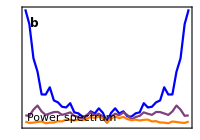

```mathematica
plotPspec=ListLinePlot[specData,
PlotRange->All,
PlotStyle->Thread@{colFun1[#]&/@plotTimesUnit},
LabelStyle->ls,
Frame->True,
AxesOrigin->{0,0},
Axes->{False,False},
ImagePadding->{{5,6*padRight},{padBottom,40}},
ImageSize->200,
AspectRatio->0.7,
FrameLabel->{{None,None},{None,"Frequency, ω"}},
PlotRangeClipping->False,
FrameTicks->{{None,Automatic},{None,Range[-4,4,1]}},
PlotLegends->Placed[lineLegend,Scaled[{0.8,0.7}]],
Epilog->{
Text[Style["Power spectrum",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

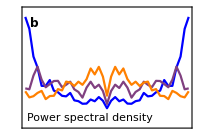

```mathematica
plotPspecNorm=ListLinePlot[specNormData,
PlotRange->{-0.02,0.14},
PlotStyle->Thread@{colFun1[#]&/@plotTimesUnit},
LabelStyle->ls,
Frame->True,
AxesOrigin->{0,0},
Axes->{False,False},
ImagePadding->{{5,6*padRight},{padBottom,40}},
ImageSize->200,
AspectRatio->0.7,
FrameLabel->{{None,None},{None,"Frequency, ω"}},
PlotRangeClipping->False,
FrameTicks->{{None,Range[-1,1,0.02]},{None,Range[-4,4,1]}},
PlotLegends->Placed[lineLegend,Scaled[{0.75,0.8}]],
Epilog->{
Text[Style["Power spectral density",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

## Grid Plot

```mathematica
cm=72/2.54;
```

### Dimensions of Plot

```mathematica
(* Horizontal dimensions *)
leftPad=1.2cm;
widthEws=12.05cm;
widthBox=5cm;
rightPad=1.2cm;
(* Total horizontal dimension *)
imWidth=leftPad+widthEws+widthBox+rightPad;

(* Vertical dimensions *)
bottomPad=1.2cm;
heightEws=2.2cm;
heightBif=3.5cm;
gapVert=0.2cm;
topPad=1.5cm;
(* Total vertical dimension *)
imHeight=bottomPad+7*heightEws+heightBif+7*gapVert+topPad;
```

### Construct grid plot

```mathematica
plotGrid=Graphics[{
(* 1st (bottom) row *)
Inset[Show[plotSmaxVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{bottomPad,0}}],{0,0},{Left,Bottom},{widthEws+leftPad,heightEws+bottomPad}],
Inset[Show[boxSmaxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{bottomPad,0}}],{widthEws+leftPad,0},{Left,Bottom},{widthBox+rightPad,heightEws+bottomPad}],
(* 2nd row *)
Inset[Show[plotKurt,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+heightEws+gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxKurt,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+heightEws+gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 3rd row *)
Inset[Show[plotSkew,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxSkew,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 4th row *)
Inset[Show[plotAc2,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxAc2,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 5th row *)
Inset[Show[plotAc1,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxAc1,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 6th row *)
Inset[Show[plotCv,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+5*heightEws+5*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxCv,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+5*heightEws+5*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 7th row *)
Inset[Show[plotVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+6*heightEws+6*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+6*heightEws+6*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 8th (top) row  *)
Inset[Show[plotTraj,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,topPad}}],{0,bottomPad+7*heightEws+7*gapVert},{Left,Bottom},{widthEws+leftPad,heightBif+topPad}],
Inset[Show[plotPspecNorm,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,topPad}}],{leftPad+widthEws,bottomPad+7*heightEws+7*gapVert},{Left,Bottom},{widthBox+rightPad,heightBif+topPad}]
},
ImageSize->{imWidth,imHeight}];
```

### Export plot

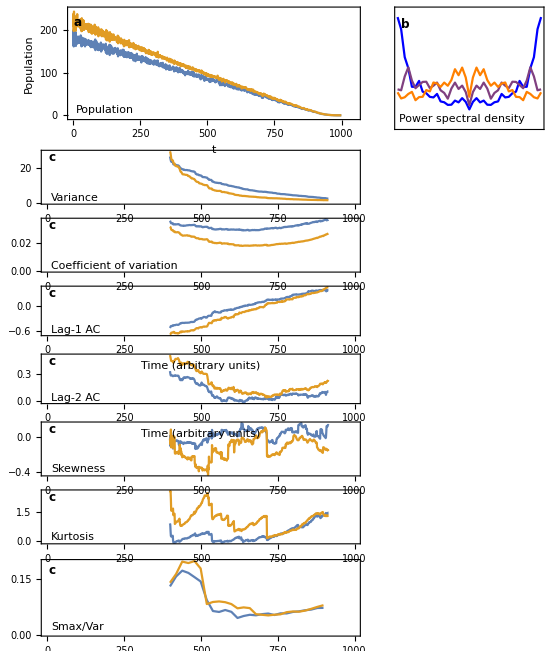

```mathematica
plotGrid
```

```mathematica
Export["figures/ews_trans_rb_long.png",plotGrid,ImageResolution->200];
```